## Plots Z-Prime Decay → neutrinos (Massive), M_Z'=10 TeV, C_ν_Ri^Z'≈ 0.1, m_ν ≈ 100 GeV (Assumed)

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

                          =  (g_PQ^2 M_(Z '))/(12π)√(1-4 m_ν^2/M_Z'^2) ( (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2-2 (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2  )

```mathematica
MassZprime10=10;
MassNu=0.1;
```

```mathematica
gVZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.1))
gAZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.0999355

-0.0000644793

```mathematica
e^2/(sinsquared(1-sinsquared))
```

0.515835

```mathematica
Zprime10decaymassNu01=MassZprime10/(12π)((gVZp01)^2+(gAZp01)^2+2(MassNu/MassZprime10)^2((gVZp01)^2-2(gAZp01)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
```

2.64916

```mathematica
Zprime10decaymassNu01NF=NumberForm[Zprime10decaymassNu01,16]
```

2.649163695931532

```mathematica
Zprime10decaymassNu01plot=MassZprime10/(12π)((GVZp01)^2+(GAZp01)^2+2(MassNu/MassZprime10)^2((GVZp01)^2-2(GAZp01)^2))√(1-4(MassNu/MassZprime10)^2)*10^3;
```

```mathematica
Plot3D[Zprime10decaymassNu01plot,{GVZp01,0,1},{GAZp01,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massive), M_Z'=8 TeV, C_ν_Ri^Z'≈ 0.1, m_ν ≈ 100 GeV (Assumed)

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

                          =  (g_PQ^2 M_(Z '))/(12π)√(1-4 m_ν^2/M_Z'^2) ( (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2-2 (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2  )

```mathematica
MassZprime8=8;
```

```mathematica
gVZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.1))
gAZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.0999355

-0.0000644793

```mathematica
Zprime8decaymassNu01=MassZprime8/(12π)((gVZp01)^2+(gAZp01)^2+2(MassNu/MassZprime8)^2((gVZp01)^2-2(gAZp01)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
```

2.11933

```mathematica
Zprime8decaymassNu01NF=NumberForm[Zprime8decaymassNu01,16]
```

2.119330773110848

```mathematica
Zprime8decaymassNu01plot=MassZprime8/(12π)((GVZp01)^2+(GAZp01)^2+2(MassNu/MassZprime8)^2((GVZp01)^2-2(GAZp01)^2))√(1-4(MassNu/MassZprime8)^2)*10^3;
```

```mathematica
Plot3D[Zprime8decaymassNu01plot,{GVZp01,0,1},{GAZp01,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massive), M_Z'=5 TeV, C_ν_Ri^Z'≈ 0.1, m_ν ≈ 100 GeV (Assumed)

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

                          =  (g_PQ^2 M_(Z '))/(12π)√(1-4 m_ν^2/M_Z'^2) ( (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2-2 (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2  )

```mathematica
MassZprime5=5;
```

```mathematica
gVZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.1))
gAZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.0999355

-0.0000644793

```mathematica
Zprime5decaymassNu01=MassZprime5/(12π)((gVZp01)^2+(gAZp01)^2+2(MassNu/MassZprime5)^2((gVZp01)^2-2(gAZp01)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
```

1.32458

```mathematica
Zprime5decaymassNu01NF=NumberForm[Zprime5decaymassNu01,16]
```

1.324580654182276

```mathematica
Zprime5decaymassNu01plot=MassZprime5/(12π)((GVZp01)^2+(GAZp01)^2+2(MassNu/MassZprime5)^2((GVZp01)^2-2(GAZp01)^2))√(1-4(MassNu/MassZprime5)^2)*10^3;
```

```mathematica
Plot3D[Zprime5decaymassNu01plot,{GVZp01,0,1},{GAZp01,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Compare Change in Z-Prime mass (massless neutrinos)

```mathematica
Zprime10decaymassless01
Zprime8decaymassless01
Zprime5decaymassless01
```

2.64916

2.11933

1.32458

```mathematica
Zprime10decaymassless01NF=NumberForm[Zprime10decaymassless01,16]
Zprime8decaymassless01NF=NumberForm[Zprime8decaymassless01,16]
Zprime5decaymassless01NF=NumberForm[Zprime5decaymassless01,16]
```

2.649163855564129

2.119331084451304

1.324581927782065

```mathematica
Zprimedecay01[Mz_]:=Mz/(12π)((gVZp01)^2+(gAZp01)^2)*10^3
```

```mathematica
Zprimedecay01[5]
Zprimedecay01[6]
Zprimedecay01[7]
Zprimedecay01[8]
Zprimedecay01[9]
Zprimedecay01[10]
Zprimedecay01[11]
Zprimedecay01[12]
```

1.32458

1.5895

1.85441

2.11933

2.38425

2.64916

2.91408

3.179

```mathematica
Zprime5decay01NF=NumberForm[Zprimedecay01[5],16]
Zprime6decay01NF=NumberForm[Zprimedecay01[6],16]
Zprime7decay01NF=NumberForm[Zprimedecay01[7],16]
Zprime8decay01NF=NumberForm[Zprimedecay01[8],16]
Zprime9decay01NF=NumberForm[Zprimedecay01[9],16]
Zprime10decay01NF=NumberForm[Zprimedecay01[10],16]
Zprime11decay01NF=NumberForm[Zprimedecay01[11],16]
Zprime12decay01NF=NumberForm[Zprimedecay01[12],16]
```

1.324581927782065

1.589498313338478

1.85441469889489

2.119331084451304

2.384247470007716

2.649163855564129

2.914080241120542

3.178996626676955

```mathematica
DecayTable01=TableForm[{{5,Zprimedecay01[5]},{6,Zprimedecay01[6]},{7,Zprimedecay01[7]},{8,Zprimedecay01[8]},{9,Zprimedecay01[9]},{10,Zprimedecay01[10]},{11,Zprimedecay01[11]},{12,Zprimedecay01[12]}},TableHeadings-> {None,{"TeV","Decay Rate(GeV)"}}]
```

TeV | Decay Rate(GeV)
5 | 1.32458
6 | 1.5895
7 | 1.85441
8 | 2.11933
9 | 2.38425
10 | 2.64916
11 | 2.91408
12 | 3.179

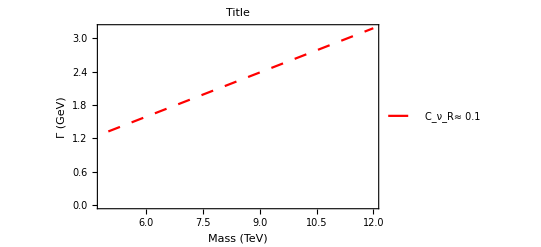

```mathematica
PlotZprimeDecay01=ListPlot[%, Joined-> True,PlotStyle->{Red,Dashing[Medium]},PlotLegends->{" C_ν_R≈ 0.1"},Frame->True,FrameLabel->{"Mass (TeV)","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
DecayTable01NF=TableForm[{{5,Zprime5decay01NF},{6,Zprime6decay01NF},{7,Zprime7decay01NF},{8,Zprime8decay01NF},{9,Zprime9decay01NF},{10,Zprime10decay01NF},{11,Zprime11decay01NF},{12,Zprime12decay01NF}},TableHeadings-> {None,{"TeV","Decay Rate (Γ → massless)"}}]
```

TeV | Decay Rate (Γ → massless)
5 | 1.324581927782065
6 | 1.589498313338478
7 | 1.85441469889489
8 | 2.119331084451304
9 | 2.384247470007716
10 | 2.649163855564129
11 | 2.914080241120542
12 | 3.178996626676955

## Compare Change in Z-Prime mass (massive neutrinos ≈ 100 GeV)

```mathematica
Zprime10decaymassNu01NF
Zprime8decaymassNu01NF
Zprime5decaymassNu01NF
```

2.649163695931532

2.119330773110848

1.324580654182276

```mathematica
ZprimedecaymassNu01[Mz_]:=Mz/(12π)((gVZp01)^2+(gAZp01)^2+2(MassNu/Mz)^2((gVZp01)^2-2(gAZp01)^2))√(1-4(MassNu/Mz)^2)*10^3;
```

```mathematica
ZprimedecaymassNu01[5]
ZprimedecaymassNu01[6]
ZprimedecaymassNu01[7]
ZprimedecaymassNu01[8]
ZprimedecaymassNu01[9]
ZprimedecaymassNu01[10]
ZprimedecaymassNu01[11]
ZprimedecaymassNu01[12]
```

1.32458

1.5895

1.85441

2.11933

2.38425

2.64916

2.91408

3.179

```mathematica
DecayTablemassNu01=TableForm[{{5,ZprimedecaymassNu01[5]},{6,ZprimedecaymassNu01[6]},{7,ZprimedecaymassNu01[7]},{8,ZprimedecaymassNu01[8]},{9,ZprimedecaymassNu01[9]},{10,ZprimedecaymassNu01[10]},{11,ZprimedecaymassNu01[11]},{12,ZprimedecaymassNu01[12]}},TableHeadings-> {None,{"TeV","Decay Rate (Γ → massive)"}}]
```

TeV | Decay Rate (Γ → massive)
5 | 1.32458
6 | 1.5895
7 | 1.85441
8 | 2.11933
9 | 2.38425
10 | 2.64916
11 | 2.91408
12 | 3.179

```mathematica
Zprime5decaymassNu01NF=NumberForm[ZprimedecaymassNu01[5],16]
Zprime6decaymassNu01NF=NumberForm[ZprimedecaymassNu01[6],16]
Zprime7decaymassNu01NF=NumberForm[ZprimedecaymassNu01[7],16]
Zprime8decaymassNu01NF=NumberForm[ZprimedecaymassNu01[8],16]
Zprime9decaymassNu01NF=NumberForm[ZprimedecaymassNu01[9],16]
Zprime10decaymassNu01NF=NumberForm[ZprimedecaymassNu01[10],16]
Zprime11decaymassNu01NF=NumberForm[ZprimedecaymassNu01[11],16]
Zprime12decaymassNu01NF=NumberForm[ZprimedecaymassNu01[12],16]
```

1.324580654182276

1.58949757608469

1.854414234413248

2.119330773110848

2.384247251198597

2.649163695931532

2.914080121084573

3.17899653413224

```mathematica
DecayTablemassNu01NF=TableForm[{{5,Zprime5decaymassNu01NF},{6,Zprime6decaymassNu01NF},{7,Zprime7decaymassNu01NF},{8,Zprime8decaymassNu01NF},{9,Zprime9decaymassNu01NF},{10,Zprime10decaymassNu01NF},{11,Zprime11decaymassNu01NF},{12,Zprime12decaymassNu01NF}},TableHeadings-> {None,{"TeV","Decay Rate (Γ → massive)"}}]
```

TeV | Decay Rate (Γ → massive)
5 | 1.324580654182276
6 | 1.58949757608469
7 | 1.854414234413248
8 | 2.119330773110848
9 | 2.384247251198597
10 | 2.649163695931532
11 | 2.914080121084573
12 | 3.17899653413224

```mathematica
PlotZprimeDecay01NFMass=ListPlot[%, Joined-> True,PlotStyle->{Red,Dashing[Medium]},PlotLegends->{" C_ν_R≈ 0.1"},Frame->True,FrameLabel->{"Mass (TeV)","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

-Graphics-

## Check for any change between massless and massive case

```mathematica
DecayTable01
DecayTablemassNu01
```

TeV | Decay Rate(GeV)
5 | 1.32458
6 | 1.5895
7 | 1.85441
8 | 2.11933
9 | 2.38425
10 | 2.64916
11 | 2.91408
12 | 3.179

TeV | Decay Rate (Γ → massive)
5 | 1.32458
6 | 1.5895
7 | 1.85441
8 | 2.11933
9 | 2.38425
10 | 2.64916
11 | 2.91408
12 | 3.179

## Compare small change in Decay Rate

```mathematica
DecayTable01NF
DecayTablemassNu01NF
```

TeV | Decay Rate (Γ → massless)
5 | 1.324581927782065
6 | 1.589498313338478
7 | 1.85441469889489
8 | 2.119331084451304
9 | 2.384247470007716
10 | 2.649163855564129
11 | 2.914080241120542
12 | 3.178996626676955

TeV | Decay Rate (Γ → massive)
5 | 1.324580654182276
6 | 1.58949757608469
7 | 1.854414234413248
8 | 2.119330773110848
9 | 2.384247251198597
10 | 2.649163695931532
11 | 2.914080121084573
12 | 3.17899653413224

## *Note each end result is multiplied by 10^3to bring Decay Rate units in MeV